## SSAMean-example.nb

LGPL Applies

```mathematica
<<xSSAlite.m
```

xSSAlite 1.2.02 (8-Nov-2011) loaded Tue-8-Nov-2011-13:34:19 using Mathematica 8.0 for Linux x86 (64-bit) (February 23, 2011)(8.0.1)

```mathematica
r={{A-> B, k1}, {B-> P, k2}, {P-> Q, k3}, {Q-> A, k4}}; 
myInitialConditions={A-> 100, B-> 0, P-> 0, Q-> 0};
myParameters={k1-> 1, k2-> 1, k3-> 1, k4-> 1};
rsim:=SSA[r, 10, myInitialConditions, myParameters, "Quiet"-> True];
```

```mathematica
sims = Table[rsim,{25}];
```

```mathematica
stats=SSAMean[sims, "Rates"-> True];
```

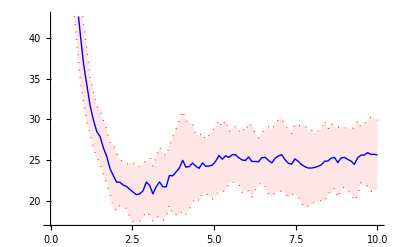

```mathematica
PlotStats[A, stats, PlotStyle-> {{Red, Dotted}, {Red, Dotted}, {Blue}}, FillingStyle-> {Opacity[.5], RGBColor[1,.9, .9]}]
```